```mathematica
h=1/√2;V[x_]:=100(ⅇ^(-2x/7.637626158259733)-2 ⅇ^(-x/7.637626158259733)+1.1845575279846237 ⅇ^(-2/3 x/7.637626158259733))
ℒ=-h^2*u''[x]+V[x]*u[x];{vals,funs}=NDEigensystem[ℒ,u[x],{x,-30,30},1,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}}}];
```

```mathematica
vals
```

{1.11637×10^-6}

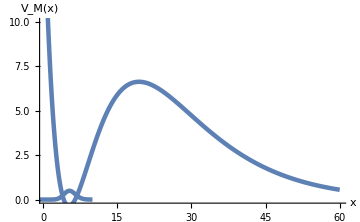

```mathematica
Show[Plot[Evaluate[h*funs+vals],{x,-10,10},BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"x","V_M(x)"},PlotPoints->1000,  PlotStyle->{Thickness[.009]}],Plot[V[x],{x,.5,60},BaseStyle->{FontWeight->"Bold", FontSize ->12}, AxesLabel->{"x","V_(x)"},PlotPoints->1000,  PlotStyle->{Thickness[.009]}],PlotRange->{{.5,60},{0,10}},AxesOrigin->{-5,0},ImageSize->Medium]
```

```mathematica
(* Now let's try the Matrix method with the osc basis 16x16 *)
```

```mathematica
s=SparseArray[{{i_,i_}->0,{i_,j_}/;i-j==-1->√(j-1)},{16,16}]
```

SparseArray[…]

```mathematica
Xosc:=1/(√2)N[s+Transpose[s]]
```

```mathematica
Posc:= ⅈ/(√2)N[(-s+Transpose[s])]
```

```mathematica
Hdarkenergyosc:= .5Posc.Posc+100(MatrixExp[-2Xosc/7.637626158259733]- 2 MatrixExp[-Xosc/7.637626158259733] + 1.184557527984623MatrixExp[-2/3 Xosc/7.637626158259733])
```

```mathematica
Reverse[N[Eigenvalues[Hdarkenergyosc]]]
```

{0.437916,2.0954,4.11158,6.48306,9.25646,12.5185,16.3977,21.0692,26.7629,33.7792,42.5208,53.552,67.7155,86.3892,112.173,151.589}

```mathematica
(* Lets try it again with 32x32 *)

s=SparseArray[{{i_,i_}->0,{i_,j_}/;i-j==-1->√(j-1)},{32,32}]
```

SparseArray[…]

```mathematica
Xosc:=1/(√2)N[s+Transpose[s]]
```

```mathematica
Posc:= ⅈ/(√2)N[(-s+Transpose[s])]
```

```mathematica
Hdarkenergyosc:= .5Posc.Posc+100(MatrixExp[-2Xosc/7.637626158259733]- 2 MatrixExp[-Xosc/7.637626158259733] + 1.184557527984623MatrixExp[-2/3 Xosc/7.637626158259733])
```

```mathematica
Reverse[N[Eigenvalues[Hdarkenergyosc]]]
```

{0.00285585,0.779618,1.65619,2.69198,3.88797,5.2333,6.7217,8.35224,10.1287,12.0595,14.1586,16.4469,18.955,21.7269,24.8229,28.3216,32.3197,36.9301,42.2814,48.5203,55.817,64.3735,74.4364,86.3132,100.397,117.206,137.443,162.103,192.688,231.653,283.649,360.363}

```mathematica
(* Lets try it again with 64x64 *)

s=SparseArray[{{i_,i_}->0,{i_,j_}/;i-j==-1->√(j-1)},{64,64}]
```

SparseArray[…]

```mathematica
Xosc:=1/(√2)N[s+Transpose[s]]
```

```mathematica
Posc:= ⅈ/(√2)N[(-s+Transpose[s])]
```

```mathematica
Hdarkenergyosc:= .5Posc.Posc+100(MatrixExp[-2Xosc/7.637626158259733]- 2 MatrixExp[-Xosc/7.637626158259733] + 1.184557527984623MatrixExp[-2/3 Xosc/7.637626158259733])
```

```mathematica
Reverse[N[Eigenvalues[Hdarkenergyosc]]]
```

{1.11711×10^-6,0.736569,1.4446,2.1235,2.77539,3.41796,4.09462,4.84283,5.67157,6.57701,7.55423,8.5995,9.71026,10.8848,12.1221,13.4215,14.783,16.2069,17.6939,19.245,20.8617,22.5459,24.3001,26.127,28.0304,30.0146,32.085,34.2484,36.5131,38.8901,41.3933,44.0418,46.8616,49.8893,53.1741,56.7785,60.7742,65.2372,70.2433,75.8679,82.1872,89.2811,97.2366,106.15,116.132,127.306,139.816,153.827,169.534,187.163,206.981,229.305,254.519,283.086,315.58,352.719,395.42,444.888,502.753,571.321,654.048,756.597,889.665,1080.19}